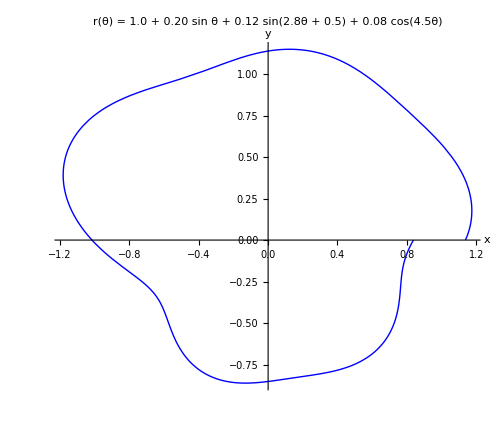

PolarPlot::optx: Unknown option Filling→Axis in PolarPlot[r[θ],{θ,0,2 π},PlotStyle→{Thick,Blue},Filling→Axis,FillingStyle→{LightBlue,Opacity[0.5]},AxesLabel→{x,y},PlotLabel→Filled Polar Shape,ImageSize→500].

PolarPlot[r[θ],{θ,0,2 π},PlotStyle→{Thick,Blue},Filling→Axis,FillingStyle→{LightBlue,Opacity[0.5]},AxesLabel→{x,y},PlotLabel→Filled Polar Shape,ImageSize→500]

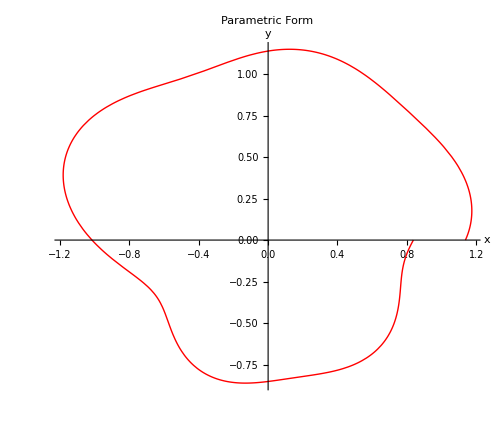

PolarPlot::optx: Unknown option Filling→Axis in PolarPlot[r[θ],{θ,0,2 π},PlotStyle→{Thick,Blue},Filling→Axis,FillingStyle→{LightBlue,Opacity[0.5]},AxesLabel→{x,y},PlotLabel→Filled Polar Shape,ImageSize→500].

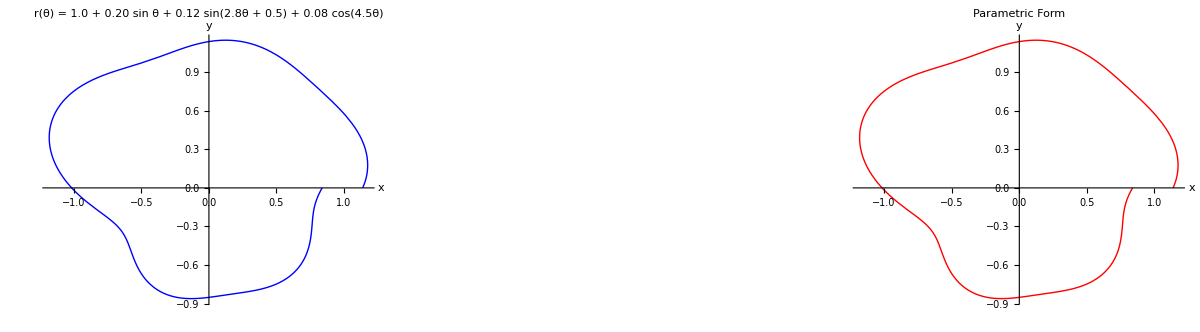

```mathematica
(*Define the radial function*)r[θ_]:=1.0+0.20 Sin[θ]+0.12 Sin[2.8 θ+0.5]+0.08 Cos[4.5 θ]

(*Create the polar plot*)
polarPlot=PolarPlot[r[θ],{θ,0,2π},PlotStyle->{Thick,Blue},AxesLabel->{"x","y"},PlotLabel->"r(θ) = 1.0 + 0.20 sin θ + 0.12 sin(2.8θ + 0.5) + 0.08 cos(4.5θ)",LabelStyle->{14,Bold},ImageSize->500]

(*Create a filled version (solid shape)*)
filledShape=PolarPlot[r[θ],{θ,0,2π},PlotStyle->{Thick,Blue},Filling->Axis,FillingStyle->{LightBlue,Opacity[0.5]},AxesLabel->{"x","y"},PlotLabel->"Filled Polar Shape",ImageSize->500]

(*Create a parametric representation for more control*)
parametricShape=ParametricPlot[{r[θ] Cos[θ],r[θ] Sin[θ]},{θ,0,2π},PlotStyle->{Red,Thick},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotLabel->"Parametric Form",ImageSize->500]

(*Display all three visualizations*)
GraphicsGrid[{{polarPlot,filledShape,parametricShape}},ImageSize->1200,Spacings->{20,0}]
```